# Connected Graph Sampler

## Prerequisites

To use the ConnectedGraphSampler package, you need:

Mathematica 10.0.2 or later.

A C++ compiler that supports the C++14 standard.

The LTemplate package. See https://github.com/szhorvat/LTemplate for installation instructions.

To check if Mathematica is already set up to use your installed C compiler, verify that the following does not return an empty list:

```mathematica
Needs["CCompilerDriver`"]
CCompilers[]
```

If LTemplate is correctly installed, evaluating the following will not result in any error messages:

```mathematica
Needs["LTemplate`"]
```

## Getting started

Add the package to the search path and load the package. The first time it is loaded, the C++ component will be automatically compiled.

```mathematica
$packagePath=FileNameJoin[{NotebookDirectory[],"."}];
If[Not@MemberQ[$Path,$packagePath],AppendTo[$Path,$packagePath]];

Get["ConnectedGraphSampler`"]
```

If compilation has failed, the most likely causes are: (1) The LTemplate package was not installed (2) No suitable C++ compiler is present on the system.

Use ? to obtain information about the symbols provided by the package:

```mathematica
?ConnectedGraphSampler`*
```

```mathematica
?CGSSample
```

CGSSample[degrees] generates a biased sample from the set of graphs with the given degrees. The result is returned in the form {graph, Log[samplingWeight]}.
CGSSample[degrees, Connected -> True] samples only connected graphs.
CGSSample[degrees, n] generates n biased samples.

## Usage

#### Basic usage

Create a single random graph with a given degree sequence. The function returns the result in the format {graph, Log[samplingWeight]}. All standard graph styling options may be used.

```mathematica
CGSSample[{3,3,2,2,1,1},
GraphStyle->"DiagramGold",VertexSize->0.6]
```

{-Graphics-,-7.67786}

Sample 6 random graphs.

```mathematica
degseq={3,3,2,2,2,2,1,1,1,1};
```

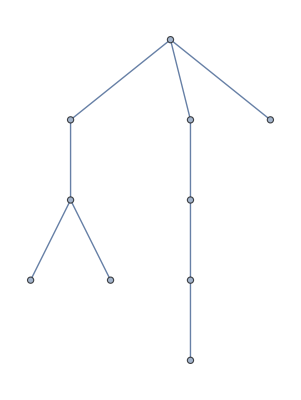
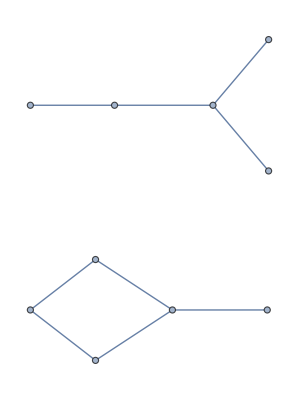
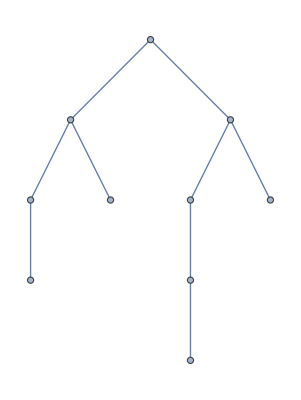
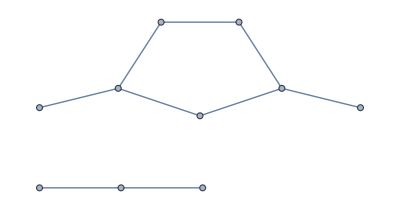
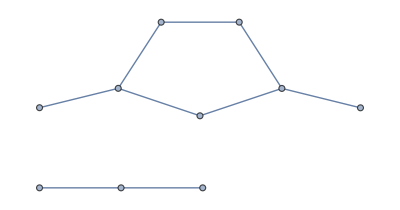
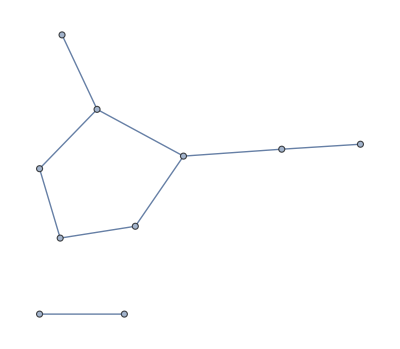
{{-Graphics-,-16.2141},{-Graphics-,-16.5344},{-Graphics-,-16.3572},{-Graphics-,-16.3572},{-Graphics-,-16.0419},{-Graphics-,-16.6116}}

```mathematica
CGSSample[degseq,6]
```

#### Connected graphs

Sample 6 connected graphs with the same degree sequence.

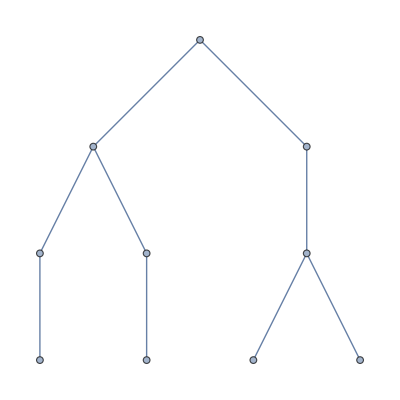
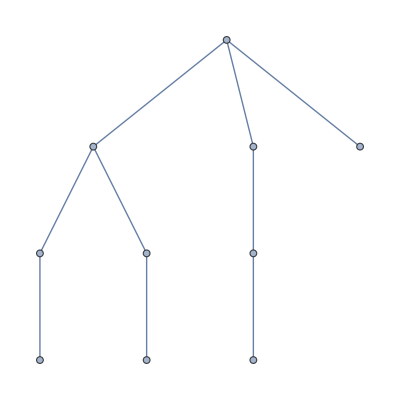
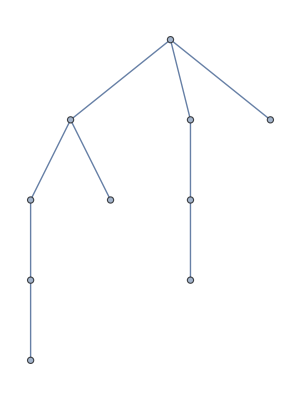
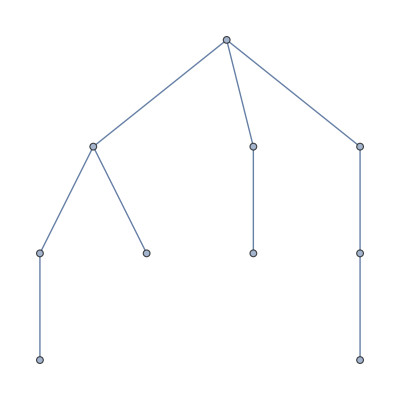
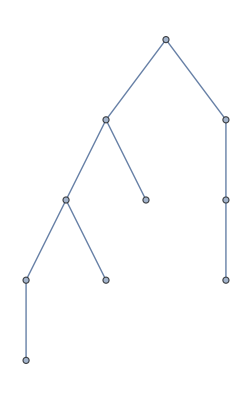
{{-Graphics-,-15.5311},{-Graphics-,-15.3851},{-Graphics-,-15.1352},{-Graphics-,-15.7722},{-Graphics-,-15.1044},{-Graphics-,-15.8463}}

```mathematica
CGSSample[degseq,6,Connected->True]
```

#### Generating samples of numerical graph properties

Sample 1000 graphs and compute their assortativity. The result is returned as a WeightedData expression:

```mathematica
sample=CGSSampleProp[degseq,GraphAssortativity,1000]
```

WeightedData[…]

Compute the mean the standard deviation of the sample:

```mathematica
{Mean[sample],StandardDeviation[sample]}
```

{-0.174627,0.289609}

Plot the histogram of assortativity values:

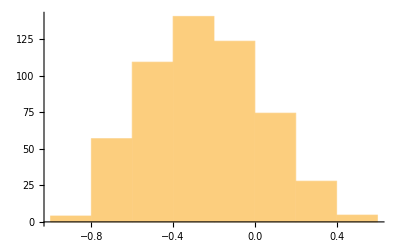

```mathematica
Histogram[sample]
```

Generate a graphical and potentially connected scale-free degree sequence;

```mathematica
SeedRandom[42]
connectedGraphicalQ=CGSPotentiallyConnectedQ[#]&&CGSGraphicalQ[#]&;
While@Not@connectedGraphicalQ[ds=Sort@RandomVariate[ZipfDistribution[1.5],100]]
```

Sample both from the set of all graphs and from the set of connected graphs, then compare the distribution of the clustering coefficient for the two cases:

```mathematica
sample1=CGSSampleProp[ds,GlobalClusteringCoefficient,10000];
sample2=CGSSampleProp[ds,GlobalClusteringCoefficient,10000,Connected->True];
```

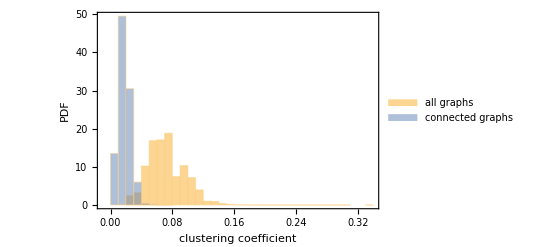

```mathematica
Histogram[{sample1,sample2},{0.01},"PDF",
Frame->True,FrameLabel->{"clustering coefficient","PDF"},
ChartLegends->{"all graphs","connected graphs"}]
```

Plot the histogram of the natural logarithm of sampling weights:

```mathematica
weights1=CGSSample[ds,10000]⟦All,2⟧;
weights2=CGSSample[ds,10000,Connected->True]⟦All,2⟧;
```

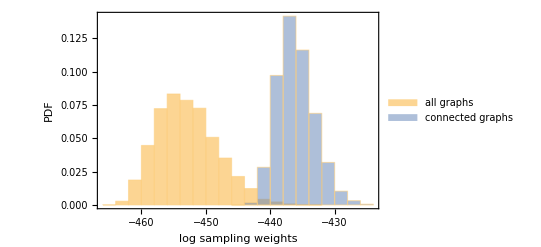

```mathematica
Histogram[{weights1,weights2},Automatic,"PDF",
Frame->True,FrameLabel->{"log sampling weights","PDF"},
ChartLegends->{"all graphs","connected graphs"}]
```

## Common options

Connected→True will sample only connected graphs.

RandomSeeding→Automatic will auto-seed the graph sampler using Mathematica’s own random number generator. This is the default. RandomSeeding→1234 will use 1234 as the seed.

Exponent→α will connect the current stub to a vertex of remaining degree d with probability proportional to d^α. Equivalently, the current stub is connected to a stub that belong to a vertex of degree d with probability proportional to d^(α-1). The default is α=1, i.e. stubs to connect to are chosen uniformly.